## Problema 3

### 3.1 Definción de la funcion de Convolución y la Función escalón unitario

La convolución de dos señales se defiene según

f*g(t)=∫_(-∞)^∞ f(τ)g(t-τ)ⅆτ

en el caso continuo y

f*g(n)=∑_(k=-∞)^∞ f(k)g(n-k)

en el caso discreto.

Definimos entonces las funciones

```mathematica
DConv:=Module[{k},Assuming[#3∈Integers,Sum[#1[k]*#2[-k+#3],{k,-Infinity,Infinity}]]&]
```

para la convolucion de señales discretas, y

```mathematica
CConv:=Module[{τ},Assuming[#3∈Reals,Integrate[#1[τ]*#2[#3-τ],{τ,-Infinity,Infinity}]]&]
```

para las señales continuas. Además resulta útil definir la función escalón unitario dada por

u(n)=Piecewise[{{1, n≥0}, {0, n<0}}]

entonces

```mathematica
u[n_]:=Piecewise[{{1,n≥0}},0]
```

Ahora aplicamos estas definiciones para resolver los ejecicios siguientes:

#### Ejecicio 3.1

Hacer la convolucion de las fuinciones

x_1(n)=(1/2)^n u(n-4)

h_1(n)=4^n u(2-n)

Definimos:

```mathematica
x1[n_]:=(1/2)^n u[n-4]
```

```mathematica
h1[n_]:=4^n u[2-n]
```

La convolución la calculamos con la funcion DConv:

```mathematica
DConv[x1, h1, n]
```

Piecewise[{{2^(9-n)/7, n>6}, {1/7 2^(-9+2 n), True}}]

entonces

y_1(n)=Piecewise[{{2^(9-n)/7, n>6}, {1/7 2^(-9+2 n), n≤6}}]

Haciendo

```mathematica
y1[n_]:=Piecewise[{{2^(9-n)/7,n>6}},2^(-9+2*n)/7]
```

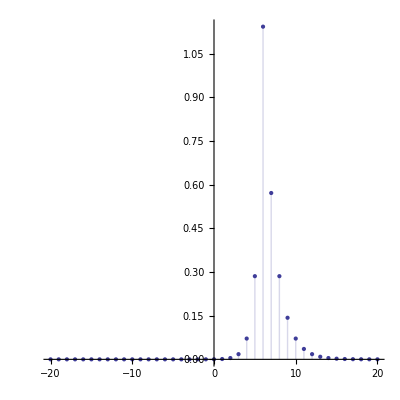

```mathematica
DiscretePlot[y1[n],{n,-20,20},AspectRatio->1,PlotRange->Full]
```

#### Ejecicio 3.2

Hacer la convolucion de las fuinciones

x_2(n)=u(-n)-u(n-2)

h_2(n)=u(n-1)-u(n-4)

Definimos:

```mathematica
x2[n_]:=u[-n]-u[-n-2]
```

```mathematica
h2[n_]:=u[n-1]-u[n-4]
```

La convolución la calculamos con la funcion DConv:

```mathematica
DConv[x2, h2, n]
```

Piecewise[{{1, n==0||n==3}, {2, 1≤n<3}, {0, True}}]

entonces

y_1(n)=Piecewise[{{1, n=1⋁n=3}, {2, 1≤n<3}, {0, n<1⋁3<n}}]

Hacemos:

```mathematica
y2[n_]:=Piecewise[{{1,n==0||n==3},{2,Inequality[1,LessEqual,n,Less,3]}},0]
```

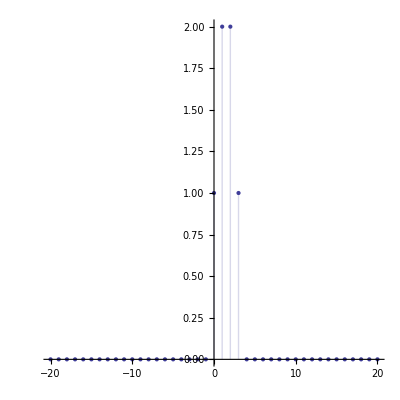

```mathematica
DiscretePlot[y2[n],{n,-20,20},AspectRatio->1,PlotRange->Full]
```

#### Ejecicio 3.3

Hacer la convolucion de las fuinciones

x_3(n)=u(n)

h_3(n)=(1/2)^-n u(-n)

Definimos:

```mathematica
x3[n_]:=u[n]
```

```mathematica
h3[n_]:=(1/2)^-n u[-n]
```

La convolución la calculamos con la funcion DConv:

```mathematica
DConv[x3, h3, n]
```

Piecewise[{{2, n>0}, {2^(1+n), True}}]

entonces

y_1(n)=Piecewise[{{2, n>0}, {2^(1+n), n≤0}}]

Haciendo:

```mathematica
y3[n_]:=Piecewise[{{2,n>0}},2^(1+n)]
```

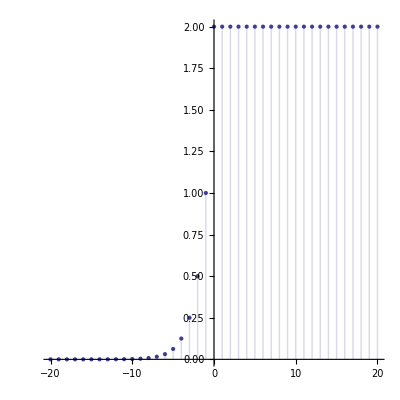

```mathematica
DiscretePlot[y3[n],{n,-20,20},AspectRatio->1,PlotRange->Full]
```

#### Ejecicio 3.4

Hacer la convolucion de las fuinciones

x_4(n)=ⅇ^(-a t)u(t)

h_4(n)=ⅇ^(-a t)u(t)

Definimos:

```mathematica
x4[t_]:=Exp[-a t]u[t]
```

```mathematica
h4[t_] := Exp[-a t] u[t]
```

En este caso las funciones son continuas por lo cual la convolución la calculamos con la funcion CConv:

```mathematica
CConv[x4, h4, t]
```

Piecewise[{{ⅇ^(-a t) t, t>0}, {0, True}}]

entonces

y_1(n)=Piecewise[{{ⅇ^(-a t) t, t>0}, {0, t≤0}}]

Haciendo:

```mathematica
y4[t_,a_]:=Piecewise[{{t/E^(a*t),t>0}},0]
```

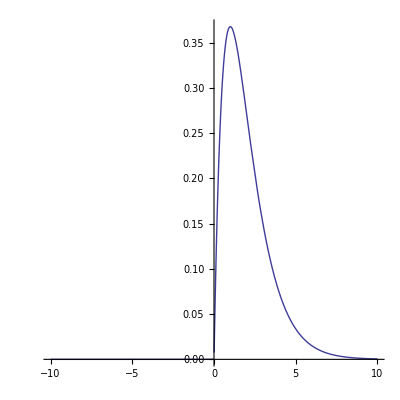

```mathematica
Plot[y4[n,1],{n,-10,10},AspectRatio->1,PlotRange->Full]
```

Para distintos valores de “a” hacemos

```mathematica
Manipulate[Plot[y4[n, a], {n,-10,10}, AspectRatio -> 1, PlotRange -> Full], {a, -10, 10, 1}]
```